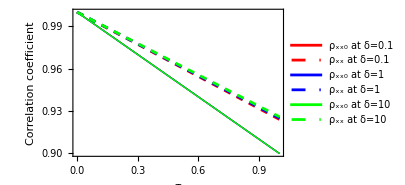
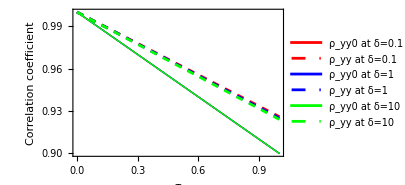
-Graphics- | -Graphics-

```mathematica
(*
This is part of the manuscript titled "Feedback-mediated circulation and persistence of stochastic fluctuations in gene
regulatory circuits" ;

Correspondence with the paper;

Please note ;
1. The four TNF motifs: Double positive feedback (++), Double negative feedback (--), Negative positive feedback (-+) and Positive negative feedback (+-);
2. αx and αy are production rates of X and Y;
3. βx and βy are degradation rates of X and Y;
4. fx=αx*gx, fy=αy*gy are the Hill functions with Hill coefficient=1;
5. xdot and ydot are the dynamical equations of X and Y;
6. xav=<x>, yav=<y> ;
7. fxyp = ∂fx/∂y and fyxp=∂fy/∂x are steady-state regulatory sensitivities;
8. G = H (feedback gain);
9. τxy and τyx are time-averaging factors;
10. δ is feedback strength and aτ is time-scale asymmetry;
11. The noise decomposition terms - intrinsic noise(xint,yint), extrinsic noise(xext,yext) and cyclic noise(xcy,ycy) are analytically derived from solving the Lyapunov equation to get the moments and then defining noise as dimensionless squared coefficient of variation;
12. ρxx0 and ρyy0 denote no-feedback autocorrelations of X and Y;
13. ρxx=ρxx0+ρxx1 and ρyy=ρyy0+ρyy1 are autocorrelations of X and Y for the TNF motifs;
14. The data is exported and plotted in another software 
====================================================================== 
*)

(* Double Positive Feedback *)

gx=y/(y+Kyx);gy=x/(x+Kxy); (*Functions*)

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

(*fixed points*)
xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fx=αx*gx; fy=αy*gy;

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;(*Derivative of functions fx, fy*)

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=(fxyp*fyxp)/(βx*βy); (*Feedback gain*)

(*Noise Decomposition*)
xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Autocorrelation *)
σxy2= ((fyxp*xav + fxyp* yav)*βx*βy)/((βx+βy)*(-fxyp*fyxp+βx*βy)); (* Covariance *)
σxx2=xtot*xav^2;
σyy2=ytot*yav^2;
ρxx0 = (1-βx*τ) ;
ρxx1= (fxyp*τ*σxy2)/σxx2;
ρyy0=(1-βy*τ) ;
ρyy1= (fyxp*τ*σxy2)/σyy2;

(* parameters for correlation by varying δ=0.1,1,10 *)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

τi=0;τf = 1;

δ=0.1;
corxx01=ρxx0;
corxx11=ρxx0+ρxx1;
coryy01=ρyy0;
coryy11=ρyy0+ρyy1;
Clear[δ]

δ=1;
corxx02=ρxx0;
corxx12=ρxx0+ρxx1;
coryy02=ρyy0;
coryy12=ρyy0+ρyy1;
Clear[δ]

δ=10;
corxx03=ρxx0;
corxx13=ρxx0+ρxx1;
coryy03=ρyy0;
coryy13=ρyy0+ρyy1;
Clear[δ]

p9=Plot[{corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_xx0 at δ=0.1","ρ_xx at δ=0.1","ρ_xx0 at δ=1","ρ_xx at δ=1","ρ_xx0 at δ=10","ρ_xx at δ=10"},PlotRange->All];
t9=Table[{τ,corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf,0.01}];
tp9=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t9];
(*Export["D:\\nashitarahman\\DP9new.dat",tp9,"FieldSeparators"->"    "];*)

p10=Plot[{coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_yy0 at δ=0.1","ρ_yy at δ=0.1","ρ_yy0 at δ=1","ρ_yy at δ=1","ρ_yy0 at δ=10","ρ_yy at δ=10"},PlotRange->All];
t10=Table[{τ,coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf,0.01}];
tp10=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t10];
(*Export["D:\\nashitarahman\\DP10new.dat",tp10,"FieldSeparators"->"    "];*)

Grid[{{p9,p10}}]

Quit[];
```

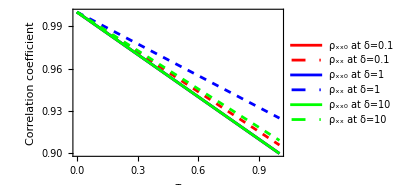
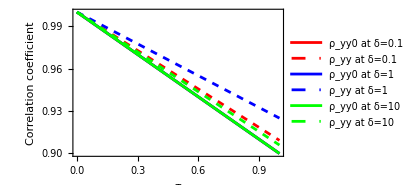
-Graphics- | -Graphics-

```mathematica
(*Double negative feedback*)
gx=Kyx/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[1,1]];
yav=y/.sol[[1,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Autocorrelation *)
σxy2= ((fyxp*xav + fxyp* yav)*βx*βy)/((βx+βy)*(-fxyp*fyxp+βx*βy)); (* Covariance *)
σxx2=xtot*xav^2;
σyy2=ytot*yav^2;
ρxx0 = (1-βx*τ) ;
ρxx1= (fxyp*τ*σxy2)/σxx2;
ρyy0=(1-βy*τ) ;
ρyy1= (fyxp*τ*σxy2)/σyy2;

(* parameters for correlation by varying δ=0.1,1,10 *)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

τi=0; τf= 1;

δ=0.1;
corxx01=ρxx0;
corxx11=ρxx0+ρxx1;
coryy01=ρyy0;
coryy11=ρyy0+ρyy1;
Clear[δ]

δ=1;
corxx02=ρxx0;
corxx12=ρxx0+ρxx1;
coryy02=ρyy0;
coryy12=ρyy0+ρyy1;
Clear[δ]

δ=10;
corxx03=ρxx0;
corxx13=ρxx0+ρxx1;
coryy03=ρyy0;
coryy13=ρyy0+ρyy1;
Clear[δ]

p9=Plot[{corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_xx0 at δ=0.1","ρ_xx at δ=0.1","ρ_xx0 at δ=1","ρ_xx at δ=1","ρ_xx0 at δ=10","ρ_xx at δ=10"},PlotRange->All];
t9=Table[{τ,corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf,0.01}];
tp9=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t9];
(*Export["D:\\nashitarahman\\DN9new.dat",tp9,"FieldSeparators"->"    "];*)

p10=Plot[{coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_yy0 at δ=0.1","ρ_yy at δ=0.1","ρ_yy0 at δ=1","ρ_yy at δ=1","ρ_yy0 at δ=10","ρ_yy at δ=10"},PlotRange->All];
t10=Table[{τ,coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf,0.01}];
tp10=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t10];
(*Export["D:\\nashitarahman\\DN10new.dat",tp10,"FieldSeparators"->"    "];*)

Grid[{{p9,p10}}]

Quit[];
```

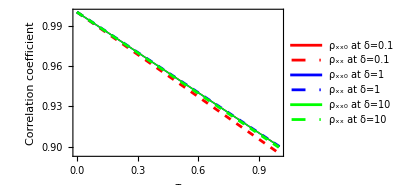
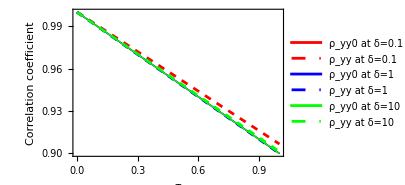
-Graphics- | -Graphics-

```mathematica
(*Negative positive feedback*)

gx=y/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Autocorrelation *)
σxy2= ((fyxp*xav + fxyp* yav)*βx*βy)/((βx+βy)*(-fxyp*fyxp+βx*βy)); (* Covariance *)
σxx2=xtot*xav^2;
σyy2=ytot*yav^2;
ρxx0 = (1-βx*τ) ;
ρxx1= (fxyp*τ*σxy2)/σxx2;
ρyy0=(1-βy*τ) ;
ρyy1= (fyxp*τ*σxy2)/σyy2;

(* parameters for correlation by varying δ=0.1,1,10 *)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

τi=0; τf= 1;

δ=0.1;
corxx01=ρxx0;
corxx11=ρxx0+ρxx1;
coryy01=ρyy0;
coryy11=ρyy0+ρyy1;
Clear[δ]

δ=1;
corxx02=ρxx0;
corxx12=ρxx0+ρxx1;
coryy02=ρyy0;
coryy12=ρyy0+ρyy1;
Clear[δ]

δ=10;
corxx03=ρxx0;
corxx13=ρxx0+ρxx1;
coryy03=ρyy0;
coryy13=ρyy0+ρyy1;
Clear[δ]

p9=Plot[{corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_xx0 at δ=0.1","ρ_xx at δ=0.1","ρ_xx0 at δ=1","ρ_xx at δ=1","ρ_xx0 at δ=10","ρ_xx at δ=10"},PlotRange->All];
t9=Table[{τ,corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf,0.01}];
tp9=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t9];
(*Export["D:\\nashitarahman\\NP9new.dat",tp9,"FieldSeparators"->"    "];*)

p10=Plot[{coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_yy0 at δ=0.1","ρ_yy at δ=0.1","ρ_yy0 at δ=1","ρ_yy at δ=1","ρ_yy0 at δ=10","ρ_yy at δ=10"},PlotRange->All];
t10=Table[{τ,coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf,0.01}];
tp10=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t10];
(*Export["D:\\nashitarahman\\NP10new.dat",tp10,"FieldSeparators"->"    "];*)

Grid[{{p9,p10}}]

Quit[];
```

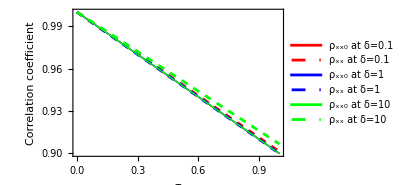
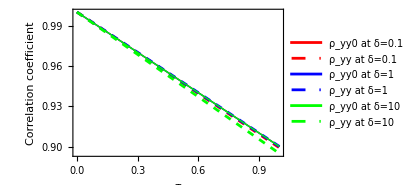
-Graphics- | -Graphics-

```mathematica
(*Positive negative feedback*)
gx=Kyx/(y+Kyx);gy=x/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Autocorrelation *)
σxy2= ((fyxp*xav + fxyp* yav)*βx*βy)/((βx+βy)*(-fxyp*fyxp+βx*βy)); (* Covariance *)
σxx2=xtot*xav^2;
σyy2=ytot*yav^2;
ρxx0 = (1-βx*τ) ;
ρxx1= (fxyp*τ*σxy2)/σxx2;
ρyy0=(1-βy*τ) ;
ρyy1= (fyxp*τ*σxy2)/σyy2;

(* parameters for correlation by varying δ=0.1,1,5,10 *)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

τi=0; τf= 1;

δ=0.1;
corxx01=ρxx0;
corxx11=ρxx0+ρxx1;
coryy01=ρyy0;
coryy11=ρyy0+ρyy1;
Clear[δ]

δ=1;
corxx02=ρxx0;
corxx12=ρxx0+ρxx1;
coryy02=ρyy0;
coryy12=ρyy0+ρyy1;
Clear[δ]

δ=10;
corxx03=ρxx0;
corxx13=ρxx0+ρxx1;
coryy03=ρyy0;
coryy13=ρyy0+ρyy1;
Clear[δ]

p9=Plot[{corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_xx0 at δ=0.1","ρ_xx at δ=0.1","ρ_xx0 at δ=1","ρ_xx at δ=1","ρ_xx0 at δ=10","ρ_xx at δ=10"},PlotRange->All];
t9=Table[{τ,corxx01,corxx11,corxx02,corxx12,corxx03,corxx13},{τ,τi,τf,0.01}];
tp9=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t9];
(*Export["D:\\nashitarahman\\PN9new.dat",tp9,"FieldSeparators"->"    "];*)

p10=Plot[{coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Red,Dashed},{Blue,Thick},{Blue,Dashed},{Green,Thick},{Green,Dashed}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"τ","Correlation coefficient"},ImageSize->300,PlotLegends->{"ρ_yy0 at δ=0.1","ρ_yy at δ=0.1","ρ_yy0 at δ=1","ρ_yy at δ=1","ρ_yy0 at δ=10","ρ_yy at δ=10"},PlotRange->All];
t10=Table[{τ,coryy01,coryy11,coryy02,coryy12,coryy03,coryy13},{τ,τi,τf,0.01}];
tp10=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[6]]]<>"   "<>toEString[#[[7]]]<>"\n"]&/@t10];
(*Export["D:\\nashitarahman\\PN10new.dat",tp10,"FieldSeparators"->"    "];*)

Grid[{{p9,p10}}]

Quit[];
```